```mathematica
Clear["Global`*"]
```

# 本征值

```mathematica
H=Normal[({{λV+λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]], t[1+2 Cos[kx/2] Cos[(√3 ky)/2]+2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]], 0, λR[Cos[kx/2] Sin[(√3 ky)/2]+√3 Sin[kx/2] Sin[(√3 ky)/2]-ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2])]}, {t[1+2 Cos[kx/2] Cos[(√3 ky)/2]-2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]], -λV-λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]], λR[Cos[kx/2] Sin[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2]+ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]+√3 Sin[kx/2] Sin[(√3 ky)/2])], 0}, {0, λR[Cos[kx/2] Sin[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2]-ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]+√3 Sin[kx/2] Sin[(√3 ky)/2])], λV-λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]], t[1+2 Cos[kx/2] Cos[(√3 ky)/2]+2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]]}, {λR[Cos[kx/2] Sin[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2]+ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2])], 0, t[1+2 Cos[kx/2] Cos[(√3 ky)/2]-2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]], -λV+λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]]}})]
```

(λV+λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]] | t[1+2 Cos[kx/2] Cos[(√3 ky)/2]+2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]] | 0 | λR[Cos[kx/2] Sin[(√3 ky)/2]+√3 Sin[kx/2] Sin[(√3 ky)/2]-ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2])]
t[1+2 Cos[kx/2] Cos[(√3 ky)/2]-2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]] | -λV-λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]] | λR[Cos[kx/2] Sin[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2]+ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]+√3 Sin[kx/2] Sin[(√3 ky)/2])] | 0
0 | λR[Cos[kx/2] Sin[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2]-ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]+√3 Sin[kx/2] Sin[(√3 ky)/2])] | λV-λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]] | t[1+2 Cos[kx/2] Cos[(√3 ky)/2]+2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]]
λR[Cos[kx/2] Sin[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2]+ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2])] | 0 | t[1+2 Cos[kx/2] Cos[(√3 ky)/2]-2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]] | -λV+λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]])

## 定义窗口Map

```mathematica
SubMovingMap[f_,list_,n_]:=Module[{len},len=Length[list];Map[f[Sequence@@Table[list[[#+i]],{i,0,n-1}]]&,Table[i,{i,1,len-n+1}]]]
```

```mathematica
MovingMapAt[f_,list_,n_,lev_]:=Piecewise[{{Map[SubMovingMap[f,#,n]&,Level[list,lev-1]],lev>=2},{SubMovingMap[f,list,n],lev==1}}]
```

```mathematica
MovingMapAt[(#1-#2)&,{{1,2,4},{4,5,6},{7,8,9}},2,2]
```

(-1 | -2
-1 | -1
-1 | -1)

## 开始处理公式

```mathematica
$Post:=If[MatrixQ[#],MatrixForm[#],#]&
```

```mathematica
hh=H/.{i->I,Subscript[x_,y_]:>ToExpression[ToString[x]<>ToString[y]]}/.{S λO->λSO}/.I[x_]->I (x)
```

(λV+λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]] | t[1+2 Cos[kx/2] Cos[(√3 ky)/2]+2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]] | 0 | λR[Cos[kx/2] Sin[(√3 ky)/2]+√3 Sin[kx/2] Sin[(√3 ky)/2]-ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2])]
t[1+2 Cos[kx/2] Cos[(√3 ky)/2]-2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]] | -λV-λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]] | λR[Cos[kx/2] Sin[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2]+ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]+√3 Sin[kx/2] Sin[(√3 ky)/2])] | 0
0 | λR[Cos[kx/2] Sin[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2]-ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]+√3 Sin[kx/2] Sin[(√3 ky)/2])] | λV-λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]] | t[1+2 Cos[kx/2] Cos[(√3 ky)/2]+2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]]
λR[Cos[kx/2] Sin[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2]+ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2])] | 0 | t[1+2 Cos[kx/2] Cos[(√3 ky)/2]-2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]] | -λV+λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]])

```mathematica
hh
```

(λV+λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]] | t[1+2 Cos[kx/2] Cos[(√3 ky)/2]+2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]] | 0 | λR[Cos[kx/2] Sin[(√3 ky)/2]+√3 Sin[kx/2] Sin[(√3 ky)/2]-ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2])]
t[1+2 Cos[kx/2] Cos[(√3 ky)/2]-2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]] | -λV-λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]] | λR[Cos[kx/2] Sin[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2]+ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]+√3 Sin[kx/2] Sin[(√3 ky)/2])] | 0
0 | λR[Cos[kx/2] Sin[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2]-ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]+√3 Sin[kx/2] Sin[(√3 ky)/2])] | λV-λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]] | t[1+2 Cos[kx/2] Cos[(√3 ky)/2]+2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]]
λR[Cos[kx/2] Sin[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2]+ⅈ (1-Cos[kx/2] Cos[(√3 ky)/2]-√3 Sin[kx/2] Sin[(√3 ky)/2])] | 0 | t[1+2 Cos[kx/2] Cos[(√3 ky)/2]-2 ⅈ Cos[kx/2] Sin[(√3 ky)/2]] | -λV+λSO[-4 Cos[(√3 ky)/2] Sin[kx/2]+2 Sin[kx]])

```mathematica
hh/.{kx->4,ky->0,λSO->0.06,λR->0.05,t->1,λV->0.4}//N
```

(0.4+0.06[-5.15079] | 1.[0.167706] | 0. | 0.05[0.-1.41615 ⅈ]
1.[0.167706] | -0.4-1. 0.06[-5.15079] | 0.05[0.+1.41615 ⅈ] | 0.
0. | 0.05[0.-1.41615 ⅈ] | 0.4-1. 0.06[-5.15079] | 1.[0.167706]
0.05[0.+1.41615 ⅈ] | 0. | 1.[0.167706] | -0.4+0.06[-5.15079])

```mathematica
hhh=hh/.{kx->4,ky->0,λSO->0.06,λR->0.05,t->1,λV->0.4}/.{x_[y_]:>x (y)}
```

(0.0909523 | 1+2 Cos[2] | 0 | 0.-0.0708073 ⅈ
1+2 Cos[2] | -0.0909523 | 0.+0.0708073 ⅈ | 0
0 | 0.-0.0708073 ⅈ | 0.709048 | 1+2 Cos[2]
0.+0.0708073 ⅈ | 0 | 1+2 Cos[2] | -0.709048)

```mathematica
Eigenvalues[hhh]
```

{0.734664,-0.734664,-0.193824,0.193824}

## 定义将分段直线化为参数方程的函数

```mathematica
F={0,0,0};
M=2Pi/a {1/Sqrt[3],0,0};
K=2Pi/a {1/Sqrt[3],1/3,0};
```

```mathematica
Line[{F,M,K,F}]/.a->1//Graphics3D
```

-Graphics3D-

编写一个函数来将直线化为参数方程：

```mathematica
ToParametric[x_,y_,d_][t_]:=Module[{len,arg},len=RegionMeasure[Line[{x,y}]];
arg={VectorAngle[y-x,{1,0,0}],VectorAngle[y-x,{0,1,0}],VectorAngle[y-x,{0,0,1}]};
Return[ConditionalExpression[t Cos[arg],0+d<t<len+d]]]
```

```mathematica
ToParametric[{0,0,0},{1,1,1},2][t]
```

ConditionalExpression[{t/(√3),t/(√3),t/(√3)}, 2<t<2+√3]

```mathematica
Clear[ToParametricMult]
```

```mathematica
ToParametricMult[x__][t_]:=Module[{new,ang,len,lenn},
new=Differences[{x}];
ang=Map[Function[a,Map[Function[b,VectorAngle[a,b]],{{1,0,0},{0,1,0},{0,0,1}}]],new];
len=Map[RegionMeasure,MovingMapAt[Line[{#1,#2}]&,{x},2,1]];
lenn=Join[{0},Accumulate[len]];
Return[Piecewise[Table[{{x}[[i]]+(t-lenn[[i]]) Cos[ang[[i]]],lenn[[i]]<t<lenn[[i+1]]},{i,1,Length[ang]}]]]
]
```

```mathematica
ToParametricMult[{0,0,0},{1,1,1},{2,1,2}][t]
```

Piecewise[{{{t/(√3),t/(√3),t/(√3)}, 0<t<√3}, {{1+(-√3+t)/(√2),1,1+(-√3+t)/(√2)}, √3<t<√2+√3}, {0, True}}]

```mathematica
fun[t_]:=ToParametricMult[F,M,K,F][t]/.(a->1)//N
```

## 作图

```mathematica
fun[j]
```

Piecewise[{{{j,0.,0.}, 0.<j<3.6276}, {{3.6276,-3.6276+j,0.}, 3.6276<j<5.72199}, {{3.6276-0.866025 (-5.72199+j),2.0944+0.5 (5.72199-1. j),0.}, 5.72199<j<9.91078}, {0., True}}]

```mathematica
fun[9.91]
```

{0.000678995,0.000392018,0.}

```mathematica
ParametricPlot3D[{fun[t][[1]],fun[t][[2]],fun[t][[3]]},{t,0.1,9.91}]
```

-Graphics3D-

```mathematica
table=Table[{ba,Eigenvalues[hh/.{kx->fun[ba][[1]],ky->fun[ba][[2]],λSO->0.06,λR->0.05,t->1,λV->0.4}/.{x_[y_]:>x (y)}]},{ba,0.1,9,0.01}];
```

```mathematica
Riffle[table[[All,1]],table[[All,2,1]]]//Partition[#,2]&;
```

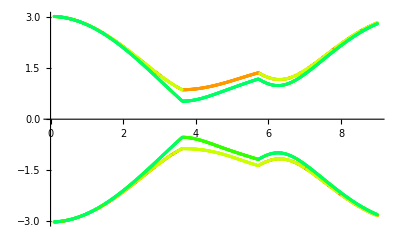

```mathematica
Table[ListPlot[Riffle[table[[All,1]],table[[All,2,i]]]//Partition[#,2]&//Re,PlotRange->All,PlotStyle->Hue[i/10]],{i,1,4}]//Show
```